```mathematica
SetDirectory[NotebookDirectory[]];
```

# Model 007

## Alternative names: ‘Model B’, ‘Ascasibar et al. model (constant τ_S)’

## Constants

```mathematica
C1=74/1000; (*[(M_(\[PermutationProduct]))^2 pc^-4 Gyr]*)
C2=360*10^-3; (*[(M_(\[PermutationProduct]))^2 pc^-4 Gyr]*)
τS=26/10;(*[Gyr]*)
Zsun=134/10000;
Zeff=Zsun*10^-3;
Zsn=9/100;
ηion=95529/100;
ηdiss=38093/100;
R=18/100;
```

## System of equations

```mathematica
(*
	Ionized gas density:        i(t) -> y[1]
	Atomic gas density:         a(t) -> y[2]
	Molecular gas density:      m(t) -> y[3]
	Metal density:              z(t) -> y[4]
	Stellar density:            s(t) -> y[5]	
     
	Each equation has Mₒ pc^(-2) Gyr^(-1)[solar_mass * parsec^(-2) * years^(-9)]
	as its units on the LHS and RHS
*)
```

```mathematica
vars={i[t],a[t],m[t],z[t],s[t]};
g=i[t]+a[t]+m[t];
tot=g+s[t];
Z=z[t]/g;
ψ=m[t]/τS;
τR=C1/(g*tot);
τC=C2/(g*tot*(Z+Zeff));
recombination=i[t]/τR;
cloudFormation=a[t]/τC;
equ= {
i'[t]==-recombination+(ηion+R)*ψ,
a'[t]==-cloudFormation+recombination+(ηdiss-ηion)*ψ,
m'[t]==cloudFormation-(1+ηdiss)*ψ,
z'[t]==(Zsn*R-Z)*ψ,
s'[t]==(1-R)*ψ
};
```

## Solving the system

### Integration span

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### Initial conditions

```mathematica
g0=148285/10000*10^-3;
i0=g0*6/10;
a0=g0*2/10;
m0=g0*2/10;
z0=g0*10^-4;
s0=g0*0;
initCond={i0,a0,m0,z0,s0};
```

### Parameters

```mathematica
params = {};
```

### Integration

```mathematica
system = Join[equ,
{
i[Tstart]==i0,
a[Tstart]==a0,
m[Tstart]==m0,
z[Tstart]==z0,
s[Tstart]==s0
}]/.params;
solutions=vars/.NDSolve[system,vars,{t,Tstart,Tend}][[1]];
```

### Save data in file

```mathematica
LogTstart=-5;
LogTend=Log10[Tend]; 
points=10^4;
times=N[Table[10^i,{i,LogTstart,LogTend,(LogTend-LogTstart)/points}],8];
```

```mathematica
denseData=Table[{N[t,6],solutions[[1]],solutions[[2]],solutions[[3]],solutions[[4]], solutions[[5]]},{t,times}];
output=Prepend[denseData,{"t    i(t)    a(t)    m(t)    z(t)    s(t)"}];
```

```mathematica
Export["plots/mathematica.dat",output,"Table"];
```

## Plots

```mathematica
igf=Table[{denseData[[i,1]],denseData[[i,2]]},{i,2,Length[denseData]}];
agf=Table[{denseData[[i,1]],denseData[[i,3]]},{i,2,Length[denseData]}];
mgf=Table[{denseData[[i,1]],denseData[[i,4]]},{i,2,Length[denseData]}];
metals=Table[{denseData[[i,1]],denseData[[i,5]]},{i,2,Length[denseData]}];
stars=Table[{denseData[[i,1]],denseData[[i,6]]},{i,2,Length[denseData]}];
```

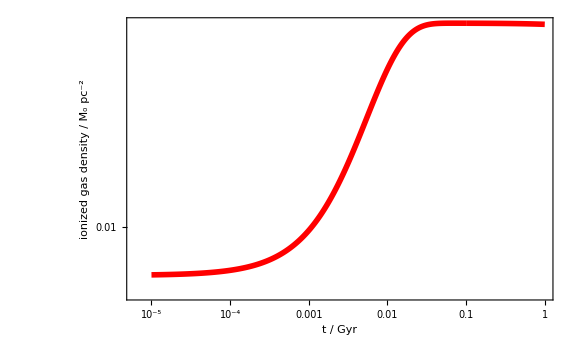

```mathematica
ListLogLogPlot[
igf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["ionized gas density / Mₒ  pc^-2",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

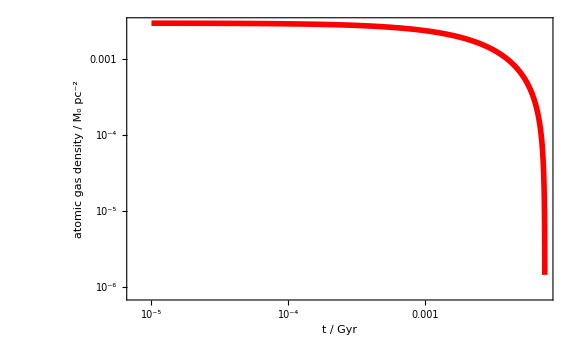

```mathematica
ListLogLogPlot[
agf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["atomic gas density / Mₒ  pc^-2",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

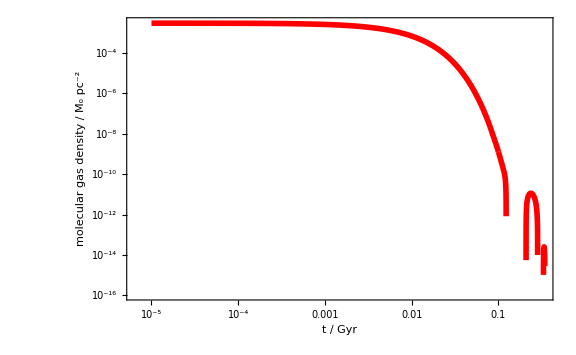

```mathematica
ListLogLogPlot[
mgf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["molecular gas density / Mₒ  pc^-2",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

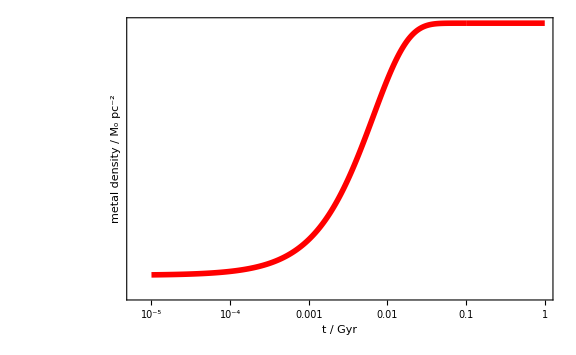

```mathematica
ListLogLogPlot[
metals,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["metal density / Mₒ  pc^-2",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

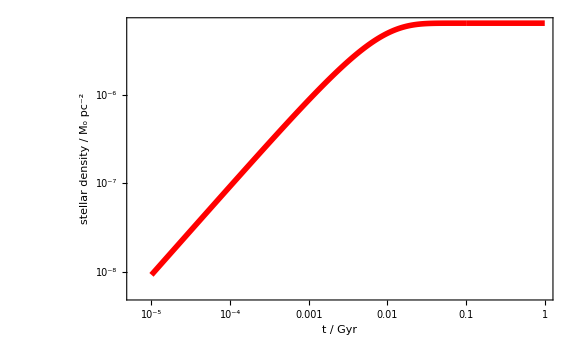

```mathematica
ListLogLogPlot[
stars,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["stellar density / Mₒ  pc^-2",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

## Jacobian matrix

### Jacobian evaluated at the initial condition

```mathematica
iniCondAss=Normal[AssociationThread[vars,initCond]];
jacobian=D[Map[(#[[2]])&,equ],{vars}]/.Join[iniCondAss,params];
ScientificForm[MatrixForm[N[jacobian,3]]]
```

(-6.54×10^-3 | -3.57×10^-3 | 3.67×10^2 | 0 | -1.78×10^-3
6.54×10^-3 | 3.57×10^-3 | -2.21×10^2 | -1.22×10^-4 | 1.78×10^-3
1.55×10^-8 | 8.48×10^-8 | -1.47×10^2 | 1.22×10^-4 | 1.39×10^-8
7.69×10^-6 | 7.69×10^-6 | 6.20×10^-3 | -7.69×10^-2 | 0
0 | 0 | 3.15×10^-1 | 0 | 0)

### Jacobian and time derivatives in C syntax

```mathematica
cStringAss=Join[
Normal[AssociationThread[
Map[ToString@*CForm,vars],
Table[ToString[y[i]],{i,0,Length[vars]-1}]
]],
{"Power(2.71828182845905,"->"exp(","Power"->"pow","Sqrt"->"sqrt"}
];
```

```mathematica
CJacobian=Map[ToString@*CForm,N[D[Map[(#[[2]])&,equ],{vars}],10],{2}];
CJacobian=Map[StringReplace[#,cStringAss]&,CJacobian];
```

```mathematica
ExpTimeJacobian =ReplaceAll[Map[(#[[2]])&,equ],Normal[AssociationMap[Head,vars]]];
CTimeDeriv=Map[ToString@*CForm,N[D[ExpTimeJacobian,t],10]];
CTimeDeriv=Map[StringReplace[#,cStringAss]&,CTimeDeriv];
```

### Jacobian for Boost odeint

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\t\tJ(``,``) = ``;\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\t\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head="/*******************************************************************************************
* Jacobian for the model 007 calculated with Wolfram Language
* and adapted for its use with the Boost odeint library.
*******************************************************************************************/

struct jacobian
{
    template <class State, class Matrix>
    void operator()(const State &y, Matrix &J, const double &t, State &dfdt)
    {
        (void)(t);\n";
tail="    }
};";
Export["jacobian_boost.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

### Jacobian for GSL

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\tgsl_matrix_set(m, ``, ``, ``);\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head=StringJoin["/*******************************************************************************************
* Jacobian for the model 007 calculated with Wolfram Language 
* and adapted for its use with the GSL library.
*******************************************************************************************/

int jacobian(double t, const double y[], double *dfdy, double dfdt[], void *params)
{
	(void)(t);
	(void)(params);\n\n",
ToString[
StringForm[
"\tgsl_matrix_view dfdy_mat = gsl_matrix_view_array(dfdy, ``, ``);\n",Length[vars],Length[vars]]],
	"\tgsl_matrix * m = &dfdy_mat.matrix;\n"];
tail="
	return GSL_SUCCESS;
};";
Export["jacobian_gsl.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

## Stiffness coefficient

```mathematica
StiffCoeff[equ_, vars_, y0_,params_]:=
Module[
{jacobian, association,Njacobian,eigenval},
jacobian=D[Map[(#[[2]])&,equ],{vars}];
association=Normal[AssociationThread[vars,y0]];
Njacobian=N[jacobian/.Join[association,params],16];
eigenval=DeleteCases[RealAbs[Re[Chop[Eigenvalues[Njacobian],10^-16]]],x_/;x==0];
Return[Max[eigenval]/Min[eigenval]];
]
```

```mathematica
StiffCoeff[equ,vars,initCond,params]
```

5.4881772090858×10^11